```mathematica
NormalDistribution[μ,σ]
```

```mathematica
PDF[NormalDistribution[μ1,σ1],x]
PDF[NormalDistribution[μ2,σ2],x]
```

(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1)

(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2)

```mathematica
f1=Function[x,(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1)][y]
```

(ⅇ^(-(y-μ1)^2/(2 σ1^2)))/(√(2 π) σ1)

```mathematica
ClearAll[f1,x,i]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
```

```mathematica
Convolve[f1[x],f2[x],x,y]
```

(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) σ1 √(1/σ1^2+1/σ2^2) σ2)

```mathematica
Simplify[(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) σ1 √(1/σ1^2+1/σ2^2) σ2)]
```

```mathematica
(ⅇ^(-(-y+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) √(σ1^2+σ2^2))
```

```mathematica
ClearAll[r]
r[x_]:=(ⅇ^(-(-x+μ1+μ2)^2/(2 (σ1^2+σ2^2))))/(√(2 π) √(σ1^2+σ2^2));
```

```mathematica
μ1=-40;
σ1=4;
μ2=-39;
σ2=2;
```

```mathematica
NIntegrate[r[x],{x,-81,-77}]
```

0.345279

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
```

```mathematica
f1[r]*f2[r+x]
```

(ⅇ^(-(r-μ1)^2/(2 σ1^2)-(r+x-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2)

```mathematica
Integrate[(ⅇ^(-(r-μ1)^2/(2 σ1^2)-(r+x-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2),{x,-ϵ,ϵ}]
```

(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (-Erf[(r-ϵ-μ2)/(√2 σ2)]+Erf[(r+ϵ-μ2)/(√2 σ2)]))/(2 √(2 π) σ1)

```mathematica
μ1=-40;
σ1=4;
μ2=-39;
σ2=2;
ϵ=3;
```

```mathematica
Integrate[(ⅇ^(-(r-μ1)^2/(2 σ1^2)-(r+x-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2),{x,0,ϵ}]
```

(ⅇ^(-1/8 (40+r)^2) (-Erf[(41+r)/(√2)]+Erf[(42+r)/(√2)]))/(4 √(2 π))

```mathematica
h[r_]:=(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (-Erf[(r-ϵ-μ2)/(√2 σ2)]+Erf[(r+ϵ-μ2)/(√2 σ2)]))/(2 √(2 π) σ1);
```

```mathematica
h[5]
```

(-Erf[41/(2 √2)]+Erf[47/(2 √2)])/(8 ⅇ^(2025/32) √(2 π))

```mathematica
NIntegrate[h[x],{x,-50,-30}]
```

0.48709

```mathematica
pic1=Plot[h[x],{x,-60,-30},PlotRange->Full];
pic2=Plot[f1[x],{x,-60,-30},PlotRange->Full];
pic3=Plot[f2[x],{x,-60,-30},PlotRange->Full];
```

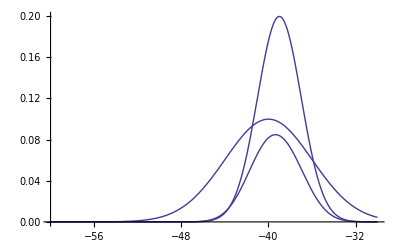

```mathematica
Show[pic3,pic2,pic1]
```

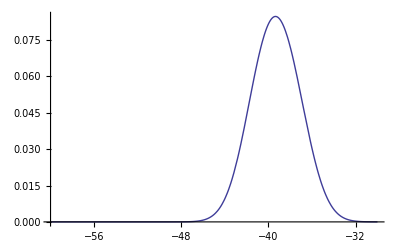

```mathematica
Plot[h[x],{x,-60,-30},PlotRange->Full]
```

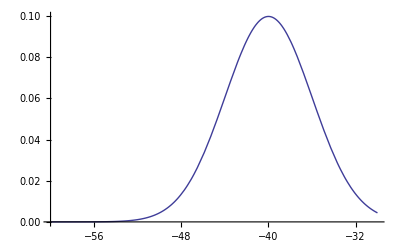

```mathematica
Plot[f1[x],{x,-60,-30},PlotRange->Full]
```

0.314453

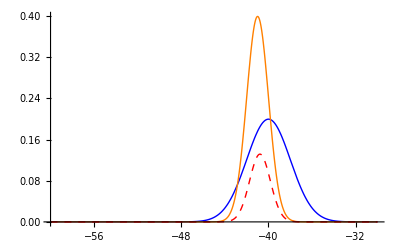

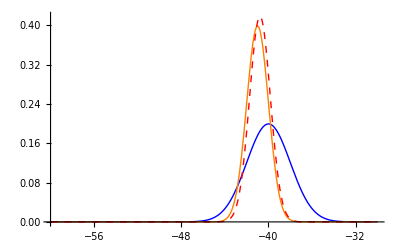

-40.

-41.

-12.8236

-40.7288

-81.

-68.1764

-40.2712

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
h[r_]:=((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (-Erf[(r-ϵ-μ1)/(√2 σ1)]+Erf[(r+ϵ-μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (-Erf[(r-ϵ-μ2)/(√2 σ2)]+Erf[(r+ϵ-μ2)/(√2 σ2)]))/σ1)/(4 √(2 π));


μ1=-40;
σ1=2;
μ2=-41;
σ2=1;
ϵ=2;


a=NIntegrate[h[x],{x,-50,-30}]
h2[x_]=h[x]/a;

Plot[{f1[x],f2[x],h[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None]
Plot[{f1[x],f2[x],h2[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None]
a1=NIntegrate[f1[x]*x,{x,-50,-30}]
a2=NIntegrate[f2[x]*x,{x,-50,-30}]
a3=NIntegrate[h[x]*x,{x,-50,-30}]
a4=NIntegrate[h2[x]*x,{x,-50,-30}]
a5=a1+a2
a6=a1+a2-a3
a7=a1+a2-a4
```

```mathematica
h2[-40]
```

0.28548

((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (Erf[(r+ϵ-μ1)/(√2 σ1)]+Erf[(-r+ϵ+μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (Erf[(r+ϵ-μ2)/(√2 σ2)]+Erf[(-r+ϵ+μ2)/(√2 σ2)]))/σ1)/(4 √(2 π))

(ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2))

(ⅇ^(-(r-μ2)^2/(2 σ2^2)) (Erf[(r+ϵ-μ1)/(√2 σ1)]+Erf[(-r+ϵ+μ1)/(√2 σ1)]))/(2 √(2 π) σ2)

(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (Erf[(r+ϵ-μ2)/(√2 σ2)]+Erf[(-r+ϵ+μ2)/(√2 σ2)]))/(2 √(2 π) σ1)

0.314453

0.314453

-Graphics-

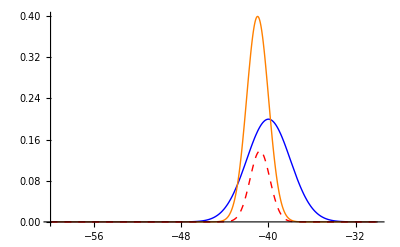

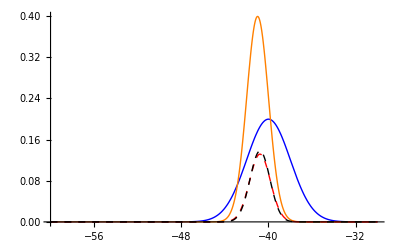

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);
h1[r_]=Integrate[(f1[r-x]*f2[r]+f1[r]*f2[r-x])/2,{x,-ϵ,ϵ}]
gg[r_]=Integrate[f1[r-x/2]*f2[r+x/2],{x,-ϵ,ϵ}]
h3[r_]=Integrate[f1[r-x]*f2[r],{x,-ϵ,ϵ}]
h4[r_]=Integrate[f2[r-x]*f1[r],{x,-ϵ,ϵ}]


h[r_]:=((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (-Erf[(r-ϵ-μ1)/(√2 σ1)]+Erf[(r+ϵ-μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (-Erf[(r-ϵ-μ2)/(√2 σ2)]+Erf[(r+ϵ-μ2)/(√2 σ2)]))/σ1)/(4 √(2 π));
μ1=-40;
σ1=2;
μ2=-41;
σ2=1;
ϵ=1;

NIntegrate[h1[x],{x,-50,-30}]
NIntegrate[gg[x],{x,-50,-30}]

Plot[{f1[x],f2[x],h1[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None]
Plot[{f1[x],f2[x],gg[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)"},LegendPosition->{1.1,-0.4},LegendShadow->None]
Plot[{f1[x],f2[x],h1[x],gg[x]},{x,-60,-30},PlotRange->Full,PlotStyle->{{Blue,Thick},{Orange,Thick},{Red,Thick,Dashed},{Black,Thick,Dashed}},PlotLegend->{"M1(h)","M2(h)","M1^M2(h)1","M1^M2(h)2"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

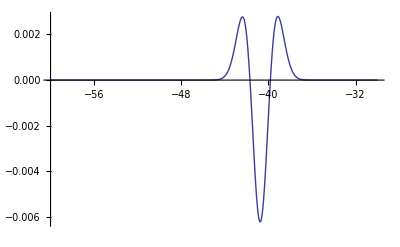

```mathematica
Plot[{h1[x]-gg[x]},{x,-60,-30},PlotRange->Full]
```

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
Simplify[((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (Erf[(r+ϵ-μ1)/(√2 σ1)]+Erf[(-r+ϵ+μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (Erf[(r+ϵ-μ2)/(√2 σ2)]+Erf[(-r+ϵ+μ2)/(√2 σ2)]))/σ1)/(4 √(2 π))]
```

```mathematica
((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (Erf[(r+ϵ-μ1)/(√2 σ1)]+Erf[(-r+ϵ+μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (Erf[(r+ϵ-μ2)/(√2 σ2)]+Erf[(-r+ϵ+μ2)/(√2 σ2)]))/σ1)/(4 √(2 π))
```

```mathematica
gg[r_]=(ⅇ^(-(-2 r+μ1+μ2)^2/(2 (σ1^2+σ2^2))) (-Erf[((2 r-ϵ-2 μ2) σ1^2-(2 r+ϵ-2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]+Erf[((2 r+ϵ-2 μ2) σ1^2+(-2 r+ϵ+2 μ1) σ2^2)/(2 √2 σ1 σ2 √(σ1^2+σ2^2))]))/(√(2 π) √(σ1^2+σ2^2));
```

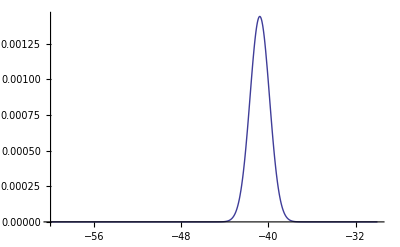

0.00322868

```mathematica
Plot[gg[x],{x,-60,-30},PlotRange->Full]
NIntegrate[gg[x],{x,-50,-30}]
```

```mathematica
NIntegrate[h1[x],{x,-45,-35}]
```

0.00322867

```mathematica
NIntegrate[(h1[x]-h2[x]),{x,-50,-30}]
NIntegrate[h1[x],{x,-50,-30}]
```

-0.685547

0.314453

```mathematica
h1[-41.]
h2[-41.]
```

0.128176

0.133803

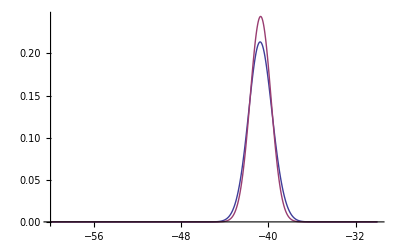

```mathematica
Plot[{h1[x],h2[x]},{x,-60,-30},PlotRange->Full]
```

```mathematica
h3[-42]
h[-42]
```

0.00585254

0.00585498

```mathematica
pic1=Plot[h[x],{x,-60,-30},PlotRange->Full,PlotStyle->{Red,Thick,Dashed}];
pic2=Plot[f1[x],{x,-60,-30},PlotRange->Full,PlotStyle->{Orange,Thick}];
pic3=Plot[f2[x],{x,-60,-30},PlotRange->Full,PlotStyle->{Blue,Thick}];

Show[pic3,pic2,pic1]
```

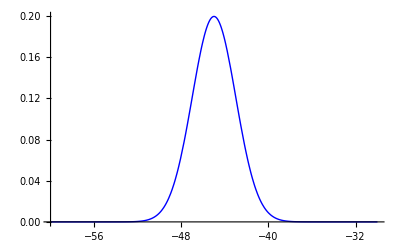

```mathematica
pic3=Plot[f2[x],{x,-60,-30},PlotRange->Full,PlotStyle->{Blue,Thick},PlotLegend->{"5k","10k","30k"},LegendPosition->{1.1,-0.4},LegendShadow->None]
```

```mathematica
ClearAll[μ1,μ2,σ1,σ2,r,ϵ,x,r]
f1[x_]:=(ⅇ^(-(x-μ1)^2/(2 σ1^2)))/(√(2 π) σ1);
f2[x_]:=(ⅇ^(-(x-μ2)^2/(2 σ2^2)))/(√(2 π) σ2);

f1[r]*f2[r+x]
f2[r]*f1[r+x]
```

(ⅇ^(-(r-μ1)^2/(2 σ1^2)-(r+x-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2)

(ⅇ^(-(r+x-μ1)^2/(2 σ1^2)-(r-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2)

```mathematica
Integrate[((ⅇ^(-(r-μ1)^2/(2 σ1^2)-(r+x-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2)+(ⅇ^(-(r+x-μ1)^2/(2 σ1^2)-(r-μ2)^2/(2 σ2^2)))/(2 π σ1 σ2))/2,{x,-ϵ,ϵ}]
```

((ⅇ^(-(r-μ2)^2/(2 σ2^2)) (-Erf[(r-ϵ-μ1)/(√2 σ1)]+Erf[(r+ϵ-μ1)/(√2 σ1)]))/σ2+(ⅇ^(-(r-μ1)^2/(2 σ1^2)) (-Erf[(r-ϵ-μ2)/(√2 σ2)]+Erf[(r+ϵ-μ2)/(√2 σ2)]))/σ1)/(4 √(2 π))

```mathematica
Erf[5]+Erf[-5]
```

0